## User choices

```mathematica
WantDetails="NoWantDetails"
```

NoWantDetails

#### Σn gives the sequence of path nodes.

```mathematica
domain[Σn_]:=Range[nMax[Σn]];
range[Σn_]:=Σn/@domain[Σn];
```

#### MONO-ORTH-TET-XISO-ISO (the BrowaeysChevrot path)

```mathematica
ΣnTETXISO[1]=TRIV;
ΣnTETXISO[2]=MONO;
ΣnTETXISO[3]=ORTH; 
ΣnTETXISO[4]=TET;  
ΣnTETXISO[5]=XISO;
ΣnTETXISO[6]=ISO;  
nMax[ΣnTETXISO]=6;
range[ΣnTETXISO]
```

{TRIV,MONO,ORTH,TET,XISO,ISO}

#### MONO-ORTH-TET-CUBE-ISO

```mathematica
ΣnTETCUBE[1]=TRIV;
ΣnTETCUBE[2]=MONO;
ΣnTETCUBE[3]=ORTH;
ΣnTETCUBE[4]=TET; 
ΣnTETCUBE[5]=CUBE;
ΣnTETCUBE[6]=ISO; 
nMax[ΣnTETCUBE]=6;
range[ΣnTETCUBE]
```

{TRIV,MONO,ORTH,TET,CUBE,ISO}

#### MONO-TRIG-CUBE-ISO

```mathematica
ΣnTRIGCUBE[1]=TRIV;
ΣnTRIGCUBE[2]=MONO;
ΣnTRIGCUBE[3]=TRIG;  
ΣnTRIGCUBE[4]=CUBE;
ΣnTRIGCUBE[5]=ISO;  
nMax[ΣnTRIGCUBE]=5;
range[ΣnTRIGCUBE]
```

{TRIV,MONO,TRIG,CUBE,ISO}

#### MONO-TRIG-XISO-ISO

```mathematica
ΣnTRIGXISO[1]=TRIV;
ΣnTRIGXISO[2]=MONO;
ΣnTRIGXISO[3]=TRIG;  
ΣnTRIGXISO[4]=XISO;
ΣnTRIGXISO[5]=ISO;  
nMax[ΣnTRIGXISO]=5;
range[ΣnTRIGXISO]
```

{TRIV,MONO,TRIG,XISO,ISO}

#### Choose Σn

```mathematica
Σn=ΣnTETCUBE;
```

```mathematica
Σn=ΣnTRIGCUBE;
```

```mathematica
Σn=ΣnTRIGXISO;
```

```mathematica
Σn=ΣnTETXISO;
```

```mathematica
ListΣ=range[Σn]
```

{TRIV,MONO,ORTH,TET,XISO,ISO}

#### Choose dt

```mathematica
dt=0.2;
```

## Section 1. Points on the path and points on the lattice. No elastic maps are involved.

```mathematica
ListSigmaAll={TRIV,MONO,ORTH,TET,XISO,ISO,TRIG,CUBE};
```

#### SYMMETRIC LATTICE Use this version for a more symmetric lattice, but not when you want beta curves.

```mathematica
ww=1.;ww=1.2;
NodePt[ISO]  :={0.,5-.5};   
NodePt[XISO]:={-1ww,4.};   
NodePt[TRIG]:={-1ww,3.};  
NodePt[CUBE]:={  1ww,4.};
NodePt[TET]  :={  1ww,3.};  
NodePt[ORTH]:={  1ww,2.};  
NodePt[MONO]:={0.,1+.5};  
NodePt[TRIV]:={0.,0+.5};  
NodePts=NodePt/@ListSigmaAll;
dummy;
```

#### ASYMMETRIC LATTICE (DEFAULT) I seem to have deleted the following paragraph and hence had to redo it, so it may be not quite what we want. But do not change it after later calculations have been made, since they would then need to be redone.

```mathematica
ww=1.;ww=1.2;
NodePt[ISO]  :={0.,5-.5};   
NodePt[XISO]:={-1ww,4.};   
NodePt[TRIG]:={-1ww,3.-.15};  (* -.15 is to discourage coincident points *)
NodePt[CUBE]:={  1ww,4.};
NodePt[TET]  :={  1ww,3.};  
NodePt[ORTH]:={  1ww,2.};  
NodePt[MONO]:={0.,1+.5};  
NodePt[TRIV]:={0.,0+.5};  
NodePts=NodePt/@ListSigmaAll;
dummy;
```

```mathematica
xyIsNodePt[{x_,y_}]:=MemberQ[NodePts,{x,y}];   (* A statement, either true or false *)
```

#### Example

```mathematica
xyIsNodePt[{0.,1.5}]
xyIsNodePt[{0.,1.7}]
```

True

False

```mathematica
LatticeBlank:={Arrowheads[.0008],Thickness[.0015],Dashing[{.013,.013}],
{Arrow[{NodePt[TRIV],NodePt[MONO]},.25]},  (* from TRIV to MONO *)
{Arrow[{NodePt[MONO],NodePt[ORTH]},.25]},  (* from MONO to ORTH *)
{Arrow[{NodePt[ORTH],NodePt[TET]},   .2]},   (* from ORTH *)
{Arrow[{NodePt[TET],  NodePt[CUBE]},.2]},   (* from TET to CUBE *)
{Arrow[{NodePt[TRIG],NodePt[XISO]},.2]},   (* from TRIG to XISO *)
{Arrow[{NodePt[TET],  NodePt[XISO]},.3]},   (* from TET to XISO *)
{Arrow[{NodePt[TRIG],NodePt[CUBE]},.3]},   (* from TRIG to CUBE *)
{Arrow[{NodePt[MONO],NodePt[TRIG]},.3]},   (* from MONO to TRIG *)
{Arrow[{NodePt[CUBE],NodePt[ISO]},.25]},   (* from CUBE to ISO *)
{Arrow[{NodePt[XISO],NodePt[ISO]},.25]}       (* from XISO to ISO *)
};
```

#### Examples.

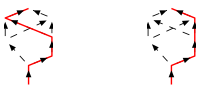

```mathematica
GraphicsRow[{
Graphics[{LatticeBlank,
{Red,Line[NodePt[ΣnTETXISO[#]]&/@domain[ΣnTETXISO]]}}],
Graphics[{LatticeBlank,
{Red,Line[NodePt[ΣnTETCUBE[#]]&/@domain[ΣnTETCUBE]]}}]},ImageSize->200,Spacings->150]
```

#### Points on the path.

```mathematica
PointsOnPath[Σn_,dt_]:=UnsortedUnion[Flatten[Table[Table[(1-t) NodePt[Σn[j]]+t NodePt[Σn[j+1]],{t,0,1,dt}],{j,1,nMax[Σn]-1}],1]];
position[point_,dt_]:=Position[AllPoints[dt],point][[1,1]];path[Σn_,dt_]:=position[#,dt]&/@PointsOnPath[Σn,dt]
```

#### Σpairs specifies the segments of the lattice to put points on. Probably you won’t have much occasion to change it. Normally it is

```mathematica
Σpairs={{TRIV,MONO},{MONO,ORTH},{MONO,TRIG},{ORTH,TET},{TET,XISO},{TET,CUBE},{XISO,ISO},{TRIG,CUBE},{TRIG,XISO},{CUBE,ISO}};
```

#### Example

```mathematica
Graphics[{LatticeBlank,
{Blue,Thickness[.02],Line[{NodePt[#[[1]]],NodePt[#[[2]]]}]}&/@Σpairs},ImageSize->100]
```

-Graphics-

#### Please do not delete this. I know you have it in BC_chooseTmat.

```mathematica
HueOfΣ[TRIV]=Gray;                       BetaText[TRIV]="β_TRIV";
HueOfΣ[MONO]=Black;                     BetaText[MONO]="β_MONO";
HueOfΣ[ORTH]=Purple;                   BetaText[ORTH]="β_ORTH";
HueOfΣ[TET]  =Blue;                        BetaText[TET]  ="β_TET";
HueOfΣ[CUBE]=Orange;                   BetaText[CUBE]="β_CUBE";
HueOfΣ[XISO]=Hue[.5,1,.7];  BetaText[XISO]="β_XISO";
HueOfΣ[ISO]  =Red;                          BetaText[ISO]   ="β_ISO";
HueOfΣ[TRIG]=Cyan;                       BetaText[TRIG] ="β_TRIG";
```

## Densify the maps on the Σpairs segments.

#### The point command is set up so that point[ {0, {Σ_1, Σ_2} } ] = NodePt[Σ_1] point[ {1, {Σ_1, Σ_2} } ] = NodePt[Σ_2]

#### Note changes here

```mathematica
point[{t_,{Σ1_,Σ2_}}]:=(1-t) NodePt[Σ1]+t NodePt[Σ2];
UnsortedPointsWithTandΣpairs[dt_]:=Flatten[Table[{point[{t,#}],t,#},{t,0,1,dt}]&/@Σpairs,1];
PointsWithTandΣpairs[dt_]:=Sort[UnsortedPointsWithTandΣpairs[dt],OrderedQ[{#1[[1]],#2[[1]]}]&];
AllPoints[dt_]:=UnsortedUnion[#[[1]]&/@PointsWithTandΣpairs[dt]];
```

```mathematica
point[{0,{Σ1,Σ2}}]== NodePt[Σ1]
point[{1,{Σ1,Σ2}}]== NodePt[Σ2]
```

True

True

#### Example.

```mathematica
(* dt=.5;*)
Graphics[{LatticeBlank,
{Blue,Thickness[.015],PointSize[.05],
Point/@AllPoints[dt],
Line[{NodePt[#[[1]]],NodePt[#[[2]]]}]}&/@Σpairs},ImageSize->100]
```

-Graphics-

#### Examples.

```mathematica
(* dt=.5;*)
ColumnForm[AllPoints[dt]]
Length[%[[1]]]
```

{-1.2,2.85}
{-1.2,3.08}
{-1.2,3.31}
{-1.2,3.54}
{-1.2,3.77}
{-1.2,4.}
{-0.96,2.58}
{-0.96,4.1}
{-0.72,2.31}
{-0.72,3.08}
{-0.72,3.8}
{-0.72,4.2}
{-0.48,2.04}
{-0.48,4.3}
{-0.24,3.6}
{-0.24,1.77}
{-0.24,3.31}
{-0.24,4.4}
{0.,0.5}
{0.,0.7}
{0.,0.9}
{0.,1.1}
{0.,1.3}
{0.,1.5}
{0.,4.5}
{0.24,4.4}
{0.24,1.6}
{0.24,3.4}
{0.24,3.54}
{0.48,4.3}
{0.48,1.7}
{0.72,3.2}
{0.72,3.77}
{0.72,4.2}
{0.72,1.8}
{0.96,1.9}
{0.96,4.1}
{1.2,2.}
{1.2,2.2}
{1.2,2.4}
{1.2,2.6}
{1.2,2.8}
{1.2,3.}
{1.2,3.2}
{1.2,3.4}
{1.2,3.6}
{1.2,3.8}
{1.2,4.}

48

```mathematica
PathSegments[Σn_]:=Table[{Σn[i],Σn[i+1]},{i,nMax[Σn]-1}];
```

```mathematica
PathSegments[ΣnTETXISO]
PathSegments[ΣnTRIGCUBE]
```

{{TRIV,MONO},{MONO,ORTH},{ORTH,TET},{TET,XISO},{XISO,ISO}}

{{TRIV,MONO},{MONO,TRIG},{TRIG,CUBE},{CUBE,ISO}}

```mathematica
PtTΣ1Σ2Triples[pt_,dt_]:=Select[PointsWithTandΣpairs[dt],#[[1]]==pt &]
```

```mathematica
ColumnForm[Table[PtTΣ1Σ2Triples[AllPoints[dt][[jj]],dt],{jj,Length[AllPoints[dt]]}]]
Length[%[[1]]]
```

{{{-1.2,2.85},1.,{MONO,TRIG}},{{-1.2,2.85},0.,{TRIG,CUBE}},{{-1.2,2.85},0.,{TRIG,XISO}}}
{{{-1.2,3.08},0.2,{TRIG,XISO}}}
{{{-1.2,3.31},0.4,{TRIG,XISO}}}
{{{-1.2,3.54},0.6,{TRIG,XISO}}}
{{{-1.2,3.77},0.8,{TRIG,XISO}}}
{{{-1.2,4.},1.,{TET,XISO}},{{-1.2,4.},0.,{XISO,ISO}},{{-1.2,4.},1.,{TRIG,XISO}}}
{{{-0.96,2.58},0.8,{MONO,TRIG}}}
{{{-0.96,4.1},0.2,{XISO,ISO}}}
{{{-0.72,2.31},0.6,{MONO,TRIG}}}
{{{-0.72,3.08},0.2,{TRIG,CUBE}}}
{{{-0.72,3.8},0.8,{TET,XISO}}}
{{{-0.72,4.2},0.4,{XISO,ISO}}}
{{{-0.48,2.04},0.4,{MONO,TRIG}}}
{{{-0.48,4.3},0.6,{XISO,ISO}}}
{{{-0.24,3.6},0.6,{TET,XISO}}}
{{{-0.24,1.77},0.2,{MONO,TRIG}}}
{{{-0.24,3.31},0.4,{TRIG,CUBE}}}
{{{-0.24,4.4},0.8,{XISO,ISO}}}
{{{0.,0.5},0.,{TRIV,MONO}}}
{{{0.,0.7},0.2,{TRIV,MONO}}}
{{{0.,0.9},0.4,{TRIV,MONO}}}
{{{0.,1.1},0.6,{TRIV,MONO}}}
{{{0.,1.3},0.8,{TRIV,MONO}}}
{{{0.,1.5},1.,{TRIV,MONO}},{{0.,1.5},0.,{MONO,ORTH}},{{0.,1.5},0.,{MONO,TRIG}}}
{{{0.,4.5},1.,{XISO,ISO}},{{0.,4.5},1.,{CUBE,ISO}}}
{{{0.24,4.4},0.8,{CUBE,ISO}}}
{{{0.24,1.6},0.2,{MONO,ORTH}}}
{{{0.24,3.4},0.4,{TET,XISO}}}
{{{0.24,3.54},0.6,{TRIG,CUBE}}}
{{{0.48,4.3},0.6,{CUBE,ISO}}}
{{{0.48,1.7},0.4,{MONO,ORTH}}}
{{{0.72,3.2},0.2,{TET,XISO}}}
{{{0.72,3.77},0.8,{TRIG,CUBE}}}
{{{0.72,4.2},0.4,{CUBE,ISO}}}
{{{0.72,1.8},0.6,{MONO,ORTH}}}
{{{0.96,1.9},0.8,{MONO,ORTH}}}
{{{0.96,4.1},0.2,{CUBE,ISO}}}
{{{1.2,2.},1.,{MONO,ORTH}},{{1.2,2.},0.,{ORTH,TET}}}
{{{1.2,2.2},0.2,{ORTH,TET}}}
{{{1.2,2.4},0.4,{ORTH,TET}}}
{{{1.2,2.6},0.6,{ORTH,TET}}}
{{{1.2,2.8},0.8,{ORTH,TET}}}
{{{1.2,3.},1.,{ORTH,TET}},{{1.2,3.},0.,{TET,XISO}},{{1.2,3.},0.,{TET,CUBE}}}
{{{1.2,3.2},0.2,{TET,CUBE}}}
{{{1.2,3.4},0.4,{TET,CUBE}}}
{{{1.2,3.6},0.6,{TET,CUBE}}}
{{{1.2,3.8},0.8,{TET,CUBE}}}
{{{1.2,4.},1.,{TET,CUBE}},{{1.2,4.},1.,{TRIG,CUBE}},{{1.2,4.},0.,{CUBE,ISO}}}

48

```mathematica
UniqueTΣ1Σ2PtTriple[pt_,dt_,Σn_]:=If[Length[PtTΣ1Σ2Triples[pt,dt]]==1,PtTΣ1Σ2Triples[pt,dt][[1]],
If[Select[PtTΣ1Σ2Triples[pt,dt],MemberQ[PathSegments[Σn],#[[3]]]&]!={},Select[PtTΣ1Σ2Triples[pt,dt],MemberQ[PathSegments[Σn],#[[3]]]&&#[[2]]==1.&][[1]],
If[Select[PtTΣ1Σ2Triples[pt,dt],#[[2]]==1.&]!={},Select[PtTΣ1Σ2Triples[pt,dt],#[[2]]==1.&][[1]],
Select[PtTΣ1Σ2Triples[pt,dt],#[[2]]==0.&]]]];
```

```mathematica
dt
range[Σn]
ColumnForm[{PaddedForm[position[#,dt],2],
PaddedForm[#,{3,2}]&/@UniqueTΣ1Σ2PtTriple[#,dt,Σn][[1]],
PaddedForm[UniqueTΣ1Σ2PtTriple[#,dt,Σn][[2]],{2,1}],
UniqueTΣ1Σ2PtTriple[#,dt,Σn][[3]]}&/@AllPoints[dt]]
```

0.2

{TRIV,MONO,ORTH,TET,XISO,ISO}

{  1,{-1.20, 2.85}, 1.0,{MONO,TRIG}}
{  2,{-1.20, 3.08}, 0.2,{TRIG,XISO}}
{  3,{-1.20, 3.31}, 0.4,{TRIG,XISO}}
{  4,{-1.20, 3.54}, 0.6,{TRIG,XISO}}
{  5,{-1.20, 3.77}, 0.8,{TRIG,XISO}}
{  6,{-1.20, 4.00}, 1.0,{TET,XISO}}
{  7,{-0.96, 2.58}, 0.8,{MONO,TRIG}}
{  8,{-0.96, 4.10}, 0.2,{XISO,ISO}}
{  9,{-0.72, 2.31}, 0.6,{MONO,TRIG}}
{ 10,{-0.72, 3.08}, 0.2,{TRIG,CUBE}}
{ 11,{-0.72, 3.80}, 0.8,{TET,XISO}}
{ 12,{-0.72, 4.20}, 0.4,{XISO,ISO}}
{ 13,{-0.48, 2.04}, 0.4,{MONO,TRIG}}
{ 14,{-0.48, 4.30}, 0.6,{XISO,ISO}}
{ 15,{-0.24, 3.60}, 0.6,{TET,XISO}}
{ 16,{-0.24, 1.77}, 0.2,{MONO,TRIG}}
{ 17,{-0.24, 3.31}, 0.4,{TRIG,CUBE}}
{ 18,{-0.24, 4.40}, 0.8,{XISO,ISO}}
{ 19,{ 0.00, 0.50}, 0.0,{TRIV,MONO}}
{ 20,{ 0.00, 0.70}, 0.2,{TRIV,MONO}}
{ 21,{ 0.00, 0.90}, 0.4,{TRIV,MONO}}
{ 22,{ 0.00, 1.10}, 0.6,{TRIV,MONO}}
{ 23,{ 0.00, 1.30}, 0.8,{TRIV,MONO}}
{ 24,{ 0.00, 1.50}, 1.0,{TRIV,MONO}}
{ 25,{ 0.00, 4.50}, 1.0,{XISO,ISO}}
{ 26,{ 0.24, 4.40}, 0.8,{CUBE,ISO}}
{ 27,{ 0.24, 1.60}, 0.2,{MONO,ORTH}}
{ 28,{ 0.24, 3.40}, 0.4,{TET,XISO}}
{ 29,{ 0.24, 3.54}, 0.6,{TRIG,CUBE}}
{ 30,{ 0.48, 4.30}, 0.6,{CUBE,ISO}}
{ 31,{ 0.48, 1.70}, 0.4,{MONO,ORTH}}
{ 32,{ 0.72, 3.20}, 0.2,{TET,XISO}}
{ 33,{ 0.72, 3.77}, 0.8,{TRIG,CUBE}}
{ 34,{ 0.72, 4.20}, 0.4,{CUBE,ISO}}
{ 35,{ 0.72, 1.80}, 0.6,{MONO,ORTH}}
{ 36,{ 0.96, 1.90}, 0.8,{MONO,ORTH}}
{ 37,{ 0.96, 4.10}, 0.2,{CUBE,ISO}}
{ 38,{ 1.20, 2.00}, 1.0,{MONO,ORTH}}
{ 39,{ 1.20, 2.20}, 0.2,{ORTH,TET}}
{ 40,{ 1.20, 2.40}, 0.4,{ORTH,TET}}
{ 41,{ 1.20, 2.60}, 0.6,{ORTH,TET}}
{ 42,{ 1.20, 2.80}, 0.8,{ORTH,TET}}
{ 43,{ 1.20, 3.00}, 1.0,{ORTH,TET}}
{ 44,{ 1.20, 3.20}, 0.2,{TET,CUBE}}
{ 45,{ 1.20, 3.40}, 0.4,{TET,CUBE}}
{ 46,{ 1.20, 3.60}, 0.6,{TET,CUBE}}
{ 47,{ 1.20, 3.80}, 0.8,{TET,CUBE}}
{ 48,{ 1.20, 4.00}, 1.0,{TET,CUBE}}

#### See the difference between the Σ pairs at the CUBE node in the two diagrams .

```mathematica
LatticeWithPts[dt_,Σn_]:=
Graphics[{LatticeBlank,
{Red,PointSize[.035],
Line[PointsOnPath[Σn,dt]],
Point/@PointsOnPath[Σn,dt]},  (* points on the red path *)
PointSize[.02],
Point/@AllPoints[dt],
Text[Style[position[#,dt],10],#+{.15,0}]&/@AllPoints[dt],
Text[Style[Row[UniqueTΣ1Σ2PtTriple[#,dt,Σn],"    "],10],#+{.9,0}]&/@NodePts},ImageSize->400]
```

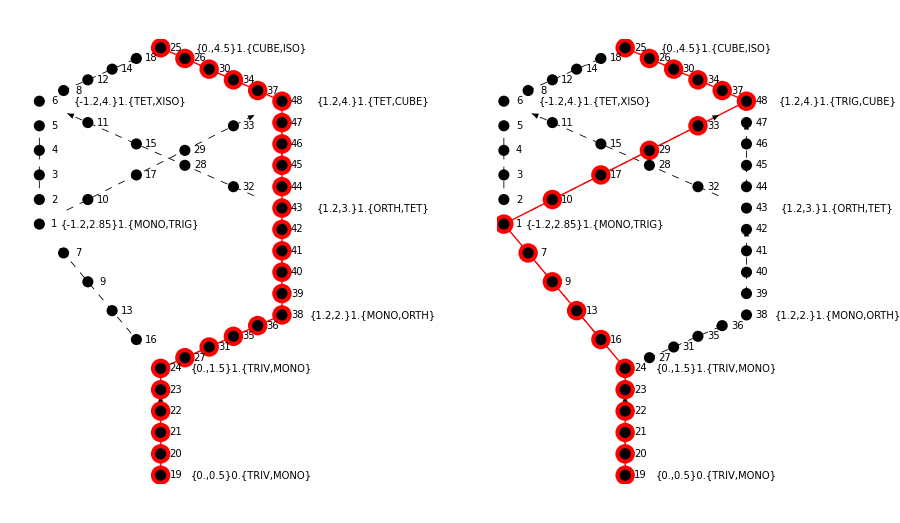

```mathematica
GraphicsRow[{LatticeWithPts[dt,ΣnTETCUBE],LatticeWithPts[dt,ΣnTRIGCUBE]},ImageSize->900]
```

```mathematica
TandΣpair[pt_,dt_]:=Select[PointsWithTandΣpairs[dt],#[[2]]==pt &][[1,1]];   
TofPt[pt_,dt_,Σn_]:=UniqueTΣ1Σ2PtTriple[pt,dt,Σn][[2]];
Σ1ofPt[pt_,dt_,Σn_]:=UniqueTΣ1Σ2PtTriple[pt,dt,Σn][[3,1]];
Σ2ofPt[pt_,dt_,Σn_]:=UniqueTΣ1Σ2PtTriple[pt,dt,Σn][[3,2]];
NodePtsOfPt[pt_,dt_,Σn_]:=NodePt/@UniqueTΣ1Σ2PtTriple[pt,dt,Σn][[3]] (* points, not symmetry clases *)
```

#### Example.

{-1.2,3.54}

0.6

{TRIG,XISO}

{{-1.2,2.85},{-1.2,4.}}

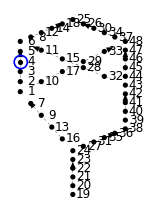

```mathematica
(* dt=.5; *)
pt=AllPoints[dt][[4]]  (* blue circle in diagram *)
TofPt[pt,dt,Σn]
{Σ1ofPt[pt,dt,Σn],Σ2ofPt[pt,dt,Σn]}
NodePtsOfPt[pt,dt,Σn]
Graphics[{LatticeBlank,
{Blue,Thickness[.008],Circle[pt,.15]},
PointSize[.025],
Point/@AllPoints[dt],
Text[Style[position[#,dt],12],#+{.25,0}]&/@AllPoints[dt]},ImageSize->150]
```

#### Example. These are the points on the path:

```mathematica
(* dt=.5 *)
range[Σn]
PointsOnPath[Σn,dt]
Length[%]
```

{TRIV,MONO,ORTH,TET,XISO,ISO}

{{0.,0.5},{0.,0.7},{0.,0.9},{0.,1.1},{0.,1.3},{0.,1.5},{0.24,1.6},{0.48,1.7},{0.72,1.8},{0.96,1.9},{1.2,2.},{1.2,2.2},{1.2,2.4},{1.2,2.6},{1.2,2.8},{1.2,3.},{0.72,3.2},{0.24,3.4},{-0.24,3.6},{-0.72,3.8},{-1.2,4.},{-0.96,4.1},{-0.72,4.2},{-0.48,4.3},{-0.24,4.4},{0.,4.5}}

26

#### The main points figure (defined above), but still no elastic maps involved.

```mathematica
LatticeWithPtsText[dt_,Σn_]:=(Print["dt = ",dt];
Print["Σn values are ",range[Σn]];
Print["All points are ",AllPoints[dt]];
Print["Number of all points is ",Length[AllPoints[dt]]];
Print["path[Σn,dt] (red) is ",path[Σn,dt]];
Print["Points on red path are ",PointsOnPath[Σn,dt]];
Print["Number of points on red path is ",Length[PointsOnPath[Σn,dt]]];)
```

#### Lattice example:

dt = 0.2

Σn values are {TRIV,MONO,ORTH,TET,XISO,ISO}

All points are {{-1.2,2.85},{-1.2,3.08},{-1.2,3.31},{-1.2,3.54},{-1.2,3.77},{-1.2,4.},{-0.96,2.58},{-0.96,4.1},{-0.72,2.31},{-0.72,3.08},{-0.72,3.8},{-0.72,4.2},{-0.48,2.04},{-0.48,4.3},{-0.24,3.6},{-0.24,1.77},{-0.24,3.31},{-0.24,4.4},{0.,0.5},{0.,0.7},{0.,0.9},{0.,1.1},{0.,1.3},{0.,1.5},{0.,4.5},{0.24,4.4},{0.24,1.6},{0.24,3.4},{0.24,3.54},{0.48,4.3},{0.48,1.7},{0.72,3.2},{0.72,3.77},{0.72,4.2},{0.72,1.8},{0.96,1.9},{0.96,4.1},{1.2,2.},{1.2,2.2},{1.2,2.4},{1.2,2.6},{1.2,2.8},{1.2,3.},{1.2,3.2},{1.2,3.4},{1.2,3.6},{1.2,3.8},{1.2,4.}}

Number of all points is 48

path[Σn,dt] (red) is {19,20,21,22,23,24,27,31,35,36,38,39,40,41,42,43,32,28,15,11,6,8,12,14,18,25}

Points on red path are {{0.,0.5},{0.,0.7},{0.,0.9},{0.,1.1},{0.,1.3},{0.,1.5},{0.24,1.6},{0.48,1.7},{0.72,1.8},{0.96,1.9},{1.2,2.},{1.2,2.2},{1.2,2.4},{1.2,2.6},{1.2,2.8},{1.2,3.},{0.72,3.2},{0.24,3.4},{-0.24,3.6},{-0.72,3.8},{-1.2,4.},{-0.96,4.1},{-0.72,4.2},{-0.48,4.3},{-0.24,4.4},{0.,4.5}}

Number of points on red path is 26

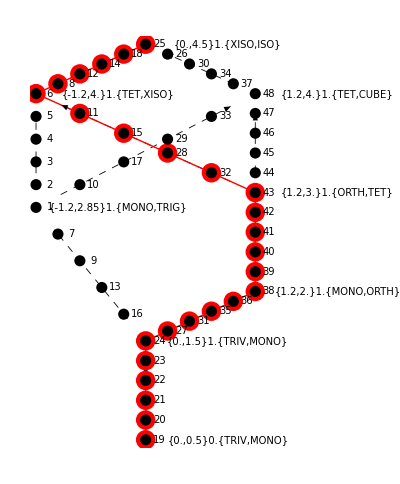

```mathematica
LatticeWithPtsText[dt,Σn]
LatticeWithPts[dt,Σn]
```

#### As functions of integer j. The integer j will give the point (j, 0) on the horizontal axis in the Beta curve diagrams. It runs over 1, 2, 3, ..., Length[path]. Not needed for the cumulative diagram or for the Lattice file. It does not involve elastic maps.

#### ΣofPt[pt, dt, Σn] is the symmetry class for the elastic map at pt, but only if pt is a node.

```mathematica
ΣofPt[pt_,dt_,Σn_]:=If[TofPt[pt,dt,Σn]==0.,Σ1ofPt[pt,dt,Σn],
                                             If[TofPt[pt,dt,Σn]==1.,Σ2ofPt[pt,dt,Σn]," "]];   
PathPtOfJ[j_,Σn_,dt_]:=PointsOnPath[Σn,dt][[j]];  
jIsNode[j_,Σn_,dt_]:=xyIsNodePt[PathPtOfJ[j,Σn,dt]];  (* A statement, either true or false *)
JlistForNodes[Σn_,dt_]:=Select[Range[Length[PointsOnPath[Σn,dt]]],jIsNode[#,Σn,dt]&];
ΣofJ[j_,Σn_,dt_]:=ΣofPt[PathPtOfJ[j,Σn,dt],dt,Σn];
```

#### Example.

```mathematica
Print["dt = ",dt];
Print["Σn values are ",range[Σn]];
PathPtOfJ[4,Σn,dt]
jIsNode[#,Σn,dt]&/@Range[Length[PointsOnPath[Σn,dt]]]
JlistForNodes[Σn,dt]
ΣofJ[#,Σn,dt]&/@Range[Length[PointsOnPath[Σn,dt]]]
```

dt = 0.2

Σn values are {TRIV,MONO,ORTH,TET,XISO,ISO}

{0.,1.1}

{True,False,False,False,False,True,False,False,False,False,True,False,False,False,False,True,False,False,False,False,True,False,False,False,False,True}

{1,6,11,16,21,26}

{TRIV, , , , ,MONO, , , , ,ORTH, , , , ,TET, , , , ,XISO, , , , ,ISO}

## Section 2. Elastic maps at nodes only. There is no dt at this stage.

#### Temporary example

```mathematica
TmatJune12=({{86, 0, 0, 0, 0, 0}, {0, 51, 0, 0, 0, 0}, {0, 0, 32, 0, 0, 0}, {0, 0, 0, 46, -20, 13}, {0, 0, 0, -20, 45, -2}, {0, 0, 0, 13, -2, 87}});
1.Eigenvalues[TmatJune12]
MatrixNote[TmatJune12]="Tmat is ORTH TmatJune12";
contours[TmatJune12]=Range[0,18,2]
MaxForScaling[TmatJune12]=17
```

{92.1724,86.,61.313,51.,32.,24.5146}

{0,2,4,6,8,10,12,14,16,18}

17

#### Choose Tmat

```mathematica
Tmat=TmatDefeat;
```

```mathematica
Tmat=TmatBrownTypo;
```

```mathematica
Tmat =TmatJune12;
```

```mathematica
Tmat=TmatIgel;
```

```mathematica
Tmat=TmatSSA2023;
```

```mathematica
Tmat=TmatMar17;
```

```mathematica
Tmat=TmatBrown;
```

#### Check for symmetry. Display output.

```mathematica
Tmat==Transpose[Tmat]
If[!(Tmat==Transpose[Tmat]),MatrixForm[Tmat-Transpose[Tmat]]]
MatrixNote[Tmat]
PrintVoigt[Tmat]
```

True

T is Brown

The [T]_𝔹𝔹 matrix is (50. | -4.8 | -14.4 | -9.3 | 10.9119 | -7.10352
-4.8 | 53.8 | 1.2 | -5.5 | -14.4915 | -2.12289
-14.4 | 1.2 | 67.2 | -5.5 | 6.63953 | -13.6355
-9.3 | -5.5 | -5.5 | 94.1 | 48.151 | 36.9873
10.9119 | -14.4915 | 6.63953 | 48.151 | 149.233 | -18.4791
-7.10352 | -2.12289 | -13.6355 | 36.9873 | -18.4791 | 189.267)

The eigenvalues are: {204.263,179.169,75.8705,60.7101,50.1339,33.4538}

The Voigt matrix is (68.3 | 32.2 | 30.4 | 4.9 | -2.3 | -0.9
32.2 | 184.3 | 5. | -4.4 | -7.8 | -6.4
30.4 | 5. | 180. | -9.2 | 7.5 | -9.4
4.9 | -4.4 | -9.2 | 25. | -2.4 | -7.2
-2.3 | -7.8 | 7.5 | -2.4 | 26.9 | 0.6
-0.9 | -6.4 | -9.4 | -7.2 | 0.6 | 33.6)

11-22-2023 16:13

𝒱_ISO(U) = 𝒱_ISO(I), independent of U, so the function U ⟶ d(T, 𝒱_ISO(U)) = d(T, 𝒯_ISO) is constant.

d(T, 𝒯_ISO) = 129.395   (Distance from T to 𝒯_ISO)

β_ISO^(□  T) = 0.454 = 26.037^o (Angle betweem T and 𝒯_ISO

P(T,𝒱_ISO(I)) = (82.8667 | 0. | 0. | 0. | 0. | 0.
0. | 82.8667 | 0. | 0. | 0. | 0.
0. | 0. | 82.8667 | 0. | 0. | 0.
0. | 0. | 0. | 82.8667 | 0. | 0.
0. | 0. | 0. | 0. | 82.8667 | 0.
0. | 0. | 0. | 0. | 0. | 189.267)  (The closest elastic map to T having symmetry ISO)

Lamé parameters for P(T,𝒱_ISO(I)) are λ = 35.4667 and μ = 41.4333, Poisson is 0.230603

#### SmatOfΣ[Σ, Tmat, Σn, nm] is the elastic map at node Σ for node mode nm. So it should have symmetry Σ The input Σn is only needed for nm = nm3. You can enter the command SmatOfΣ, but do not try to evaluate it unless you have run the appropriate OutputFor, described momentarily.

#### This is the command that allows us to unify everything.

```mathematica
SmatOfΣ[Σ_,Tmat_,dummy_,nm2]:=Closest[Tmat,Σ];
SmatOfΣ[Σ_,Tmat_,Σn_,       nm3]:=ClosestToPrior[Σ,Tmat,Σn];
SmatOfΣ[Σ_,Tmat_,dummy_,nm4]:=ProjToVSigOfU[Tmat,UforNM4,Σ];
```

```mathematica
TextNodeMode[nm2]="Node mode nm2: Closest to Tmat";
TextNodeMode[nm3]="Node mode nm3: Closest to prior";
TextNodeMode[nm4]="Node mode nm4: P(T,𝒱_Σ(U))";
```

#### For nm2. Only run if you want nm2.

```mathematica
Print[DateSequence[DateList[],"yes"]];
MatrixNote[Tmat]
OutputFor[Tmat,#]&/@ListSigmaAll
```

11-22-2023 16:13

T is Brown

11-22-2023 16:13

𝒯_TRIV = 𝒯

d(T, 𝒯_TRIV) = d(T, 𝒯) = 0 for all elastic maps T

β_TRIV^T = ∠(T, 𝒯_TRIV) = 0           ''

11-22-2023 16:13

NMinimize = {19.3941,{θ→1.68223,σ→0.319894,ϕ→2.33199}}  (minimizing the function  (θ, σ, ϕ) ⟶ d(T, 𝒱_MONO(U)), U = (Û)_S(θ,σ,ϕ))

((θ_0, σ_0, ϕ_0) in degrees are {96.4,0.,133.6})

U_0 = (Û)_S(θ_0,σ_0,ϕ_0) = (0.0767049 | -0.993798 | -0.0805105
-0.68551 | -0.111201 | 0.719521
-0.724011 | 0 | -0.689788)  (A MONO-minimizer for T. It minimizes the function  U ⟶ d(T, 𝒱_MONO(U)))

11-22-2023 16:13

NMinimize = {32.9751,{θ→1.47929,σ→-1.41812,ϕ→0.768554}}  (minimizing the function  (θ, σ, ϕ) ⟶ d(T, 𝒱_ORTH(U)), U = (Û)_S(θ,σ,ϕ))

((θ_0, σ_0, ϕ_0) in degrees are {84.8,-81.3,44.})

U_0 = (Û)_S(θ_0,σ_0,ϕ_0) = (0.994223 | -0.0865168 | 0.0635195
0.0185598 | 0.721479 | 0.692188
-0.105714 | -0.68701 | 0.718917)  (A ORTH-minimizer for T. It minimizes the function  U ⟶ d(T, 𝒱_ORTH(U)))

11-22-2023 16:13

NMinimize = {40.302,{θ→0.0454989,σ→0.0274727,ϕ→1.66271}}  (minimizing the function  (θ, σ, ϕ) ⟶ d(T, 𝒱_TET(U)), U = (Û)_S(θ,σ,ϕ))

((θ_0, σ_0, ϕ_0) in degrees are {2.6,1.6,95.3})

U_0 = (Û)_S(θ_0,σ_0,ϕ_0) = (-0.0929013 | -0.0429475 | 0.994749
0.0232679 | 0.998703 | 0.0452912
-0.995403 | 0.0273533 | -0.0917815)  (A TET-minimizer for T. It minimizes the function  U ⟶ d(T, 𝒱_TET(U)))

11-22-2023 16:14

NMinimize = {94.1024,{θ→2.76397,σ→-0.686623,ϕ→3.00954}}  (minimizing the function  (θ, σ, ϕ) ⟶ d(T, 𝒱_XISO(U)), U = (Û)_S(θ,σ,ϕ))

((θ_0, σ_0, ϕ_0) in degrees are {158.4,0.,172.4})

U_0 = (Û)_S(θ_0,σ_0,ϕ_0) = (0.921451 | -0.368714 | -0.12239
-0.365504 | -0.929543 | 0.0485472
-0.131666 | 0 | -0.991294)  (A XISO-minimizer for T. It minimizes the function  U ⟶ d(T, 𝒱_XISO(U)))

11-22-2023 16:14

𝒱_ISO(U) = 𝒱_ISO(I), independent of U, so the function U ⟶ d(T, 𝒱_ISO(U)) = d(T, 𝒯_ISO) is constant.

d(T, 𝒯_ISO) = 129.395   (Distance from T to 𝒯_ISO)

β_ISO^(□  T) = 0.454 = 26.037^o (Angle betweem T and 𝒯_ISO

P(T,𝒱_ISO(I)) = (82.8667 | 0. | 0. | 0. | 0. | 0.
0. | 82.8667 | 0. | 0. | 0. | 0.
0. | 0. | 82.8667 | 0. | 0. | 0.
0. | 0. | 0. | 82.8667 | 0. | 0.
0. | 0. | 0. | 0. | 82.8667 | 0.
0. | 0. | 0. | 0. | 0. | 189.267)  (The closest elastic map to T having symmetry ISO)

Lamé parameters for P(T,𝒱_ISO(I)) are λ = 35.4667 and μ = 41.4333, Poisson is 0.230603

11-22-2023 16:14

NMinimize = {82.3728,{θ→0.22904,σ→-0.867254,ϕ→1.33736}}  (minimizing the function  (θ, σ, ϕ) ⟶ d(T, 𝒱_TRIG(U)), U = (Û)_S(θ,σ,ϕ))

((θ_0, σ_0, ϕ_0) in degrees are {13.1,-49.7,76.6})

U_0 = (Û)_S(θ_0,σ_0,ϕ_0) = (0.318873 | 0.0249105 | 0.94747
-0.708665 | 0.670078 | 0.220885
-0.629376 | -0.741873 | 0.231323)  (A TRIG-minimizer for T. It minimizes the function  U ⟶ d(T, 𝒱_TRIG(U)))

11-22-2023 16:14

NMinimize = {106.21,{θ→0.0974921,σ→-1.53454,ϕ→1.66977}}  (minimizing the function  (θ, σ, ϕ) ⟶ d(T, 𝒱_CUBE(U)), U = (Û)_S(θ,σ,ϕ))

((θ_0, σ_0, ϕ_0) in degrees are {5.6,-87.9,95.7})

U_0 = (Û)_S(θ_0,σ_0,ϕ_0) = (0.093709 | -0.101807 | 0.990381
-0.994946 | 0.0264644 | 0.0968614
-0.036071 | -0.994452 | -0.0988123)  (A CUBE-minimizer for T. It minimizes the function  U ⟶ d(T, 𝒱_CUBE(U)))

{Null,Null,Null,Null,Null,Null,Null,Null}

#### The matrices UT[Tmat, Σ] produced by OutputFor above.

```mathematica
Print[DateSequence[DateList[],"yes"]];
MatrixNote[Tmat]
{#,MatrixForm[UT[Tmat,#]]}&/@ListSigmaAll
```

11-22-2023 16:15

T is Brown

{{TRIV,(1 | 0 | 0
0 | 1 | 0
0 | 0 | 1)},{MONO,(0.0767049 | -0.993798 | -0.0805105
-0.68551 | -0.111201 | 0.719521
-0.724011 | 0. | -0.689788)},{ORTH,(0.994223 | -0.0865168 | 0.0635195
0.0185598 | 0.721479 | 0.692188
-0.105714 | -0.68701 | 0.718917)},{TET,(-0.0929013 | -0.0429475 | 0.994749
0.0232679 | 0.998703 | 0.0452912
-0.995403 | 0.0273533 | -0.0917815)},{XISO,(0.921451 | -0.368714 | -0.12239
-0.365504 | -0.929543 | 0.0485472
-0.131666 | 0. | -0.991294)},{ISO,(1 | 0 | 0
0 | 1 | 0
0 | 0 | 1)},{TRIG,(0.318873 | 0.0249105 | 0.94747
-0.708665 | 0.670078 | 0.220885
-0.629376 | -0.741873 | 0.231323)},{CUBE,(0.093709 | -0.101807 | 0.990381
-0.994946 | 0.0264644 | 0.0968614
-0.036071 | -0.994452 | -0.0988123)}}

#### For nm3. This paragraph should be run for each path Σn that you want. Save the output for comparison later.

```mathematica
Σn
Σn/@domain[Σn]
Σn[3]
PriorΣ[Σn[3],Σn]
NextΣ[Σn[3],Σn]
```

ΣnTETXISO

{TRIV,MONO,ORTH,TET,XISO,ISO}

ORTH

MONO

TET

```mathematica
ΣnTRIGCUBE
```

ΣnTRIGCUBE

#### Needed if you have not run the nm2 above:

```mathematica
MatrixNote[Tmat]
range[Σn]
OutputFor[Tmat,Σn[1]]
```

T is Brown

{TRIV,MONO,ORTH,TET,XISO,ISO}

11-22-2023 16:15

𝒯_TRIV = 𝒯

d(T, 𝒯_TRIV) = d(T, 𝒯) = 0 for all elastic maps T

β_TRIV^T = ∠(T, 𝒯_TRIV) = 0           ''

#### This is subtle, in that each step is evaluating SmatOfΣ (via ClosestToPrior) for the next. If troubles occur, try going back to the AA file and reentering ClosestToPrior.

```mathematica
(* MatrixNote[Tmat]
range[Σn]
OutputFor[SmatOfΣ[#,Tmat,Σn,nm3],NextΣ[#,Σn]]&/@Drop[range[Σn],-1] *)
```

#### COMPUTE nm3 FOR ALL PRE-CHOSEN NODE SEQUENCES (This takes time but gives the most flexibility for later.)

```mathematica
MatrixNote[Tmat]
range[ΣnTETXISO]
OutputFor[SmatOfΣ[#,Tmat,ΣnTETXISO,nm3],NextΣ[#,ΣnTETXISO]]&/@Drop[range[ΣnTETXISO],-1]
```

T is Brown

{TRIV,MONO,ORTH,TET,XISO,ISO}

11-22-2023 16:15

NMinimize = {19.3941,{θ→1.68223,σ→0.319894,ϕ→2.33199}}  (minimizing the function  (θ, σ, ϕ) ⟶ d(T, 𝒱_MONO(U)), U = (Û)_S(θ,σ,ϕ))

((θ_0, σ_0, ϕ_0) in degrees are {96.4,0.,133.6})

U_0 = (Û)_S(θ_0,σ_0,ϕ_0) = (0.0767049 | -0.993798 | -0.0805105
-0.68551 | -0.111201 | 0.719521
-0.724011 | 0 | -0.689788)  (A MONO-minimizer for T. It minimizes the function  U ⟶ d(T, 𝒱_MONO(U)))

11-22-2023 16:15

NMinimize = {26.7156,{θ→0.013398,σ→0.804573,ϕ→1.67317}}  (minimizing the function  (θ, σ, ϕ) ⟶ d(T, 𝒱_ORTH(U)), U = (Û)_S(θ,σ,ϕ))

((θ_0, σ_0, ϕ_0) in degrees are {0.8,46.1,95.9})

U_0 = (Û)_S(θ_0,σ_0,ϕ_0) = (-0.0805105 | 0.0643378 | 0.994675
0.719521 | 0.694343 | 0.0133274
-0.689788 | 0.716762 | -0.102194)  (A ORTH-minimizer for T. It minimizes the function  U ⟶ d(T, 𝒱_ORTH(U)))

11-22-2023 16:15

NMinimize = {23.9577,{θ→0.013398,σ→0.0191751,ϕ→1.67317}}  (minimizing the function  (θ, σ, ϕ) ⟶ d(T, 𝒱_TET(U)), U = (Û)_S(θ,σ,ϕ))

((θ_0, σ_0, ϕ_0) in degrees are {0.8,1.1,95.9})

U_0 = (Û)_S(θ_0,σ_0,ϕ_0) = (-0.102423 | -0.0114358 | 0.994675
0.0178033 | 0.999753 | 0.0133275
-0.994582 | 0.0190736 | -0.102194)  (A TET-minimizer for T. It minimizes the function  U ⟶ d(T, 𝒱_TET(U)))

11-22-2023 16:16

NMinimize = {88.7118,{θ→6.11108,σ→0.111619,ϕ→0.104147}}  (minimizing the function  (θ, σ, ϕ) ⟶ d(T, 𝒱_XISO(U)), U = (Û)_S(θ,σ,ϕ))

((θ_0, σ_0, ϕ_0) in degrees are {350.1,0.,6.})

U_0 = (Û)_S(θ_0,σ_0,ϕ_0) = (0.979889 | 0.171254 | 0.102423
-0.170326 | 0.985227 | -0.0178033
-0.103959 | 0 | 0.994582)  (A XISO-minimizer for T. It minimizes the function  U ⟶ d(T, 𝒱_XISO(U)))

11-22-2023 16:16

𝒱_ISO(U) = 𝒱_ISO(I), independent of U, so the function U ⟶ d(T, 𝒱_ISO(U)) = d(T, 𝒯_ISO) is constant.

d(T, 𝒯_ISO) = 84.9089   (Distance from T to 𝒯_ISO)

β_ISO^(□  T) = 0.31 = 17.77^o (Angle betweem T and 𝒯_ISO

P(T,𝒱_ISO(I)) = (82.8667 | 0. | 0. | 0. | 0. | 0.
0. | 82.8667 | 0. | 0. | 0. | 0.
0. | 0. | 82.8667 | 0. | 0. | 0.
0. | 0. | 0. | 82.8667 | 0. | 0.
0. | 0. | 0. | 0. | 82.8667 | 0.
0. | 0. | 0. | 0. | 0. | 189.267)  (The closest elastic map to T having symmetry ISO)

Lamé parameters for P(T,𝒱_ISO(I)) are λ = 35.4667 and μ = 41.4333, Poisson is 0.230603

{Null,Null,Null,Null,Null}

```mathematica
MatrixNote[Tmat]
range[ΣnTRIGCUBE]
OutputFor[SmatOfΣ[#,Tmat,ΣnTRIGCUBE,nm3],NextΣ[#,ΣnTRIGCUBE]]&/@Drop[range[ΣnTRIGCUBE],-1]
```

T is Brown

{TRIV,MONO,TRIG,CUBE,ISO}

11-22-2023 16:16

NMinimize = {19.3941,{θ→1.68223,σ→0.319894,ϕ→2.33199}}  (minimizing the function  (θ, σ, ϕ) ⟶ d(T, 𝒱_MONO(U)), U = (Û)_S(θ,σ,ϕ))

((θ_0, σ_0, ϕ_0) in degrees are {96.4,0.,133.6})

U_0 = (Û)_S(θ_0,σ_0,ϕ_0) = (0.0767049 | -0.993798 | -0.0805105
-0.68551 | -0.111201 | 0.719521
-0.724011 | 0 | -0.689788)  (A MONO-minimizer for T. It minimizes the function  U ⟶ d(T, 𝒱_MONO(U)))

11-22-2023 16:16

NMinimize = {81.7126,{θ→0.29446,σ→0.268627,ϕ→1.38203}}  (minimizing the function  (θ, σ, ϕ) ⟶ d(T, 𝒱_TRIG(U)), U = (Û)_S(θ,σ,ϕ))

((θ_0, σ_0, ϕ_0) in degrees are {16.9,15.4,79.2})

U_0 = (Û)_S(θ_0,σ_0,ϕ_0) = (0.0961012 | -0.327473 | 0.939961
0.30649 | 0.908185 | 0.285067
-0.94701 | 0.260693 | 0.187645)  (A TRIG-minimizer for T. It minimizes the function  U ⟶ d(T, 𝒱_TRIG(U)))

11-22-2023 16:17

NMinimize = {75.8243,{θ→1.19125,σ→-0.437035,ϕ→0.824001}}  (minimizing the function  (θ, σ, ϕ) ⟶ d(T, 𝒱_CUBE(U)), U = (Û)_S(θ,σ,ϕ))

((θ_0, σ_0, ϕ_0) in degrees are {68.3,-25.,47.2})

U_0 = (Û)_S(θ_0,σ_0,ϕ_0) = (0.621153 | -0.735012 | 0.271895
0.414832 | 0.602724 | 0.681644
-0.664894 | -0.310614 | 0.67929)  (A CUBE-minimizer for T. It minimizes the function  U ⟶ d(T, 𝒱_CUBE(U)))

11-22-2023 16:17

𝒱_ISO(U) = 𝒱_ISO(I), independent of U, so the function U ⟶ d(T, 𝒱_ISO(U)) = d(T, 𝒯_ISO) is constant.

d(T, 𝒯_ISO) = 62.7752   (Distance from T to 𝒯_ISO)

β_ISO^(□  T) = 0.233 = 13.33^o (Angle betweem T and 𝒯_ISO

P(T,𝒱_ISO(I)) = (82.8667 | 0. | 0. | 0. | 0. | 0.
0. | 82.8667 | 0. | 0. | 0. | 0.
0. | 0. | 82.8667 | 0. | 0. | 0.
0. | 0. | 0. | 82.8667 | 0. | 0.
0. | 0. | 0. | 0. | 82.8667 | 0.
0. | 0. | 0. | 0. | 0. | 189.267)  (The closest elastic map to T having symmetry ISO)

Lamé parameters for P(T,𝒱_ISO(I)) are λ = 35.4667 and μ = 41.4333, Poisson is 0.230603

{Null,Null,Null,Null}

```mathematica
MatrixNote[Tmat]
range[ΣnTETCUBE]
OutputFor[SmatOfΣ[#,Tmat,ΣnTETCUBE,nm3],NextΣ[#,ΣnTETCUBE]]&/@Drop[range[ΣnTETCUBE],-1]
```

T is Brown

{TRIV,MONO,ORTH,TET,CUBE,ISO}

11-22-2023 16:17

NMinimize = {19.3941,{θ→1.68223,σ→0.319894,ϕ→2.33199}}  (minimizing the function  (θ, σ, ϕ) ⟶ d(T, 𝒱_MONO(U)), U = (Û)_S(θ,σ,ϕ))

((θ_0, σ_0, ϕ_0) in degrees are {96.4,0.,133.6})

U_0 = (Û)_S(θ_0,σ_0,ϕ_0) = (0.0767049 | -0.993798 | -0.0805105
-0.68551 | -0.111201 | 0.719521
-0.724011 | 0 | -0.689788)  (A MONO-minimizer for T. It minimizes the function  U ⟶ d(T, 𝒱_MONO(U)))

11-22-2023 16:17

NMinimize = {26.7156,{θ→0.013398,σ→0.804573,ϕ→1.67317}}  (minimizing the function  (θ, σ, ϕ) ⟶ d(T, 𝒱_ORTH(U)), U = (Û)_S(θ,σ,ϕ))

((θ_0, σ_0, ϕ_0) in degrees are {0.8,46.1,95.9})

U_0 = (Û)_S(θ_0,σ_0,ϕ_0) = (-0.0805105 | 0.0643378 | 0.994675
0.719521 | 0.694343 | 0.0133274
-0.689788 | 0.716762 | -0.102194)  (A ORTH-minimizer for T. It minimizes the function  U ⟶ d(T, 𝒱_ORTH(U)))

11-22-2023 16:18

NMinimize = {23.9577,{θ→0.013398,σ→0.0191751,ϕ→1.67317}}  (minimizing the function  (θ, σ, ϕ) ⟶ d(T, 𝒱_TET(U)), U = (Û)_S(θ,σ,ϕ))

((θ_0, σ_0, ϕ_0) in degrees are {0.8,1.1,95.9})

U_0 = (Û)_S(θ_0,σ_0,ϕ_0) = (-0.102423 | -0.0114358 | 0.994675
0.0178033 | 0.999753 | 0.0133275
-0.994582 | 0.0190736 | -0.102194)  (A TET-minimizer for T. It minimizes the function  U ⟶ d(T, 𝒱_TET(U)))

11-22-2023 16:18

NMinimize = {98.5233,{θ→0.013398,σ→0.0191751,ϕ→1.67317}}  (minimizing the function  (θ, σ, ϕ) ⟶ d(T, 𝒱_CUBE(U)), U = (Û)_S(θ,σ,ϕ))

((θ_0, σ_0, ϕ_0) in degrees are {0.8,1.1,95.9})

U_0 = (Û)_S(θ_0,σ_0,ϕ_0) = (-0.102423 | -0.0114358 | 0.994675
0.0178033 | 0.999753 | 0.0133275
-0.994582 | 0.0190736 | -0.102194)  (A CUBE-minimizer for T. It minimizes the function  U ⟶ d(T, 𝒱_CUBE(U)))

11-22-2023 16:18

𝒱_ISO(U) = 𝒱_ISO(I), independent of U, so the function U ⟶ d(T, 𝒱_ISO(U)) = d(T, 𝒯_ISO) is constant.

d(T, 𝒯_ISO) = 73.2971   (Distance from T to 𝒯_ISO)

β_ISO^(□  T) = 0.27 = 15.47^o (Angle betweem T and 𝒯_ISO

P(T,𝒱_ISO(I)) = (82.8667 | 0. | 0. | 0. | 0. | 0.
0. | 82.8667 | 0. | 0. | 0. | 0.
0. | 0. | 82.8667 | 0. | 0. | 0.
0. | 0. | 0. | 82.8667 | 0. | 0.
0. | 0. | 0. | 0. | 82.8667 | 0.
0. | 0. | 0. | 0. | 0. | 189.267)  (The closest elastic map to T having symmetry ISO)

Lamé parameters for P(T,𝒱_ISO(I)) are λ = 35.4667 and μ = 41.4333, Poisson is 0.230603

{Null,Null,Null,Null,Null}

```mathematica
MatrixNote[Tmat]
range[ΣnTRIGXISO]
OutputFor[SmatOfΣ[#,Tmat,ΣnTRIGXISO,nm3],NextΣ[#,ΣnTRIGXISO]]&/@Drop[range[ΣnTRIGXISO],-1]
```

T is Brown

{TRIV,MONO,TRIG,XISO,ISO}

11-22-2023 16:18

NMinimize = {19.3941,{θ→1.68223,σ→0.319894,ϕ→2.33199}}  (minimizing the function  (θ, σ, ϕ) ⟶ d(T, 𝒱_MONO(U)), U = (Û)_S(θ,σ,ϕ))

((θ_0, σ_0, ϕ_0) in degrees are {96.4,0.,133.6})

U_0 = (Û)_S(θ_0,σ_0,ϕ_0) = (0.0767049 | -0.993798 | -0.0805105
-0.68551 | -0.111201 | 0.719521
-0.724011 | 0 | -0.689788)  (A MONO-minimizer for T. It minimizes the function  U ⟶ d(T, 𝒱_MONO(U)))

11-22-2023 16:19

NMinimize = {81.7126,{θ→0.29446,σ→0.268627,ϕ→1.38203}}  (minimizing the function  (θ, σ, ϕ) ⟶ d(T, 𝒱_TRIG(U)), U = (Û)_S(θ,σ,ϕ))

((θ_0, σ_0, ϕ_0) in degrees are {16.9,15.4,79.2})

U_0 = (Û)_S(θ_0,σ_0,ϕ_0) = (0.0961012 | -0.327473 | 0.939961
0.30649 | 0.908185 | 0.285067
-0.94701 | 0.260693 | 0.187645)  (A TRIG-minimizer for T. It minimizes the function  U ⟶ d(T, 𝒱_TRIG(U)))

11-22-2023 16:19

NMinimize = {63.3279,{θ→0.29446,σ→-1.20852,ϕ→1.38203}}  (minimizing the function  (θ, σ, ϕ) ⟶ d(T, 𝒱_XISO(U)), U = (Û)_S(θ,σ,ϕ))

((θ_0, σ_0, ϕ_0) in degrees are {16.9,0.,79.2})

U_0 = (Û)_S(θ_0,σ_0,ϕ_0) = (0.179569 | -0.290223 | 0.939961
0.0544588 | 0.956959 | 0.285067
-0.982237 | 0 | 0.187645)  (A XISO-minimizer for T. It minimizes the function  U ⟶ d(T, 𝒱_XISO(U)))

11-22-2023 16:19

𝒱_ISO(U) = 𝒱_ISO(I), independent of U, so the function U ⟶ d(T, 𝒱_ISO(U)) = d(T, 𝒯_ISO) is constant.

d(T, 𝒯_ISO) = 75.3633   (Distance from T to 𝒯_ISO)

β_ISO^(□  T) = 0.277 = 15.88^o (Angle betweem T and 𝒯_ISO

P(T,𝒱_ISO(I)) = (82.8667 | 0. | 0. | 0. | 0. | 0.
0. | 82.8667 | 0. | 0. | 0. | 0.
0. | 0. | 82.8667 | 0. | 0. | 0.
0. | 0. | 0. | 82.8667 | 0. | 0.
0. | 0. | 0. | 0. | 82.8667 | 0.
0. | 0. | 0. | 0. | 0. | 189.267)  (The closest elastic map to T having symmetry ISO)

Lamé parameters for P(T,𝒱_ISO(I)) are λ = 35.4667 and μ = 41.4333, Poisson is 0.230603

{Null,Null,Null,Null}

#### The matrices UT[SmatOfΣ, NextΣ] produced by OutputFor above.

```mathematica
{#,Chop[MatrixForm[UT[SmatOfΣ[#,Tmat,Σn,nm3],NextΣ[#,Σn]]],0.001]}&/@Drop[Σn/@domain[Σn],-1]
```

{{TRIV,(0.0767049 | -0.993798 | -0.0805105
-0.68551 | -0.111201 | 0.719521
-0.724011 | 0 | -0.689788)},{MONO,(-0.0805105 | 0.0643378 | 0.994675
0.719521 | 0.694343 | 0.0133274
-0.689788 | 0.716762 | -0.102194)},{ORTH,(-0.102423 | -0.0114358 | 0.994675
0.0178033 | 0.999753 | 0.0133275
-0.994582 | 0.0190736 | -0.102194)},{TET,(0.979889 | 0.171254 | 0.102423
-0.170326 | 0.985227 | -0.0178033
-0.103959 | 0 | 0.994582)},{XISO,(1 | 0 | 0
0 | 1 | 0
0 | 0 | 1)}}

#### The matrices at the nodes for nm3.

```mathematica
Print[DateSequence[DateList[],"yes"]];
MatrixNote[Tmat]
Print[TextNodeMode[nm3]];
Print["Node sequence is ",Σn/@domain[Σn]];
{#,Chop[MatrixForm[SmatOfΣ[#,Tmat,Σn,nm3]],0.0001]}&/@(Σn/@domain[Σn])
```

11-22-2023 16:19

T is Brown

Node mode nm3: Closest to prior

Node sequence is {TRIV,MONO,ORTH,TET,XISO,ISO}

{{TRIV,(50. | -4.8 | -14.4 | -9.3 | 10.9119 | -7.10352
-4.8 | 53.8 | 1.2 | -5.5 | -14.4915 | -2.12289
-14.4 | 1.2 | 67.2 | -5.5 | 6.63953 | -13.6355
-9.3 | -5.5 | -5.5 | 94.1 | 48.151 | 36.9873
10.9119 | -14.4915 | 6.63953 | 48.151 | 149.233 | -18.4791
-7.10352 | -2.12289 | -13.6355 | 36.9873 | -18.4791 | 189.267)},{MONO,(48.5015 | -10.1159 | -7.74458 | -9.22251 | 9.37601 | -7.38876
-10.1159 | 61.7123 | 0.910195 | -8.9761 | -11.3441 | -3.2773
-7.74458 | 0.910195 | 59.1615 | -3.40581 | 4.3541 | -12.0748
-9.22251 | -8.9761 | -3.40581 | 96.5977 | 48.3338 | 35.6995
9.37601 | -11.3441 | 4.3541 | 48.3338 | 148.36 | -21.2519
-7.38876 | -3.2773 | -12.0748 | 35.6995 | -21.2519 | 189.267)},{ORTH,(47.3087 | -3.09908 | -1.05627 | -9.84992 | 11.085 | -8.30133
-3.09908 | 62.1997 | 2.3175 | -4.94367 | -10.8641 | 7.22046
-1.05627 | 2.3175 | 60.4795 | -2.21162 | 0.294029 | -1.79801
-9.84992 | -4.94367 | -2.21162 | 95.826 | 48.9018 | 34.886
11.085 | -10.8641 | 0.294029 | 48.9018 | 148.519 | -19.3664
-8.30133 | 7.22046 | -1.79801 | 34.886 | -19.3664 | 189.267)},{TET,(47.3843 | -0.315251 | -1.42524 | 2.43642 | 4.1673 | 0.0956792
-0.315251 | 62.0514 | 0.103913 | -5.15905 | -10.8992 | 7.14088
-1.42524 | 0.103913 | 60.4942 | -0.675366 | -0.859386 | -0.931263
2.43642 | -5.15905 | -0.675366 | 95.4268 | 48.601 | 34.7455
4.1673 | -10.8992 | -0.859386 | 48.601 | 148.977 | -19.6439
0.0956792 | 7.14088 | -0.931263 | 34.7455 | -19.6439 | 189.267)},{XISO,(54.1924 | -0.525618 | -2.42965 | 0.452524 | 2.92937 | -0.621951
-0.525618 | 57.1249 | 0.36547 | 2.27629 | -16.8528 | 3.5781
-2.42965 | 0.36547 | 77.5353 | 0.0029275 | 0.377316 | -0.0640492
0.452524 | 2.27629 | 0.0029275 | 77.5424 | 1.05256 | -0.178672
2.92937 | -16.8528 | 0.377316 | 1.05256 | 147.938 | -19.9506
-0.621951 | 3.5781 | -0.0640492 | -0.178672 | -19.9506 | 189.267)},{ISO,(82.8667 | 0 | 0 | 0 | 0 | 0
0 | 82.8667 | 0 | 0 | 0 | 0
0 | 0 | 82.8667 | 0 | 0 | 0
0 | 0 | 0 | 82.8667 | 0 | 0
0 | 0 | 0 | 0 | 82.8667 | 0
0 | 0 | 0 | 0 | 0 | 189.267)}}

#### For nm4, no OutputFor is needed here.

#### Choose U. (This UforNM4 will get used in other calculations, so be sure it is set to what you want.)

```mathematica
UforNM4=({{0, 0, 1}, {0, -1, 0}, {1, 0, 0}});
```

```mathematica
UforNM4=({{-1, 0, 0}, {0, 0, 1}, {0, 1, 0}});
```

```mathematica
UforNM4=id;
```

```mathematica
UforNM4=UT[Tmat,XISO];
```

#### The matrices at the nodes for nm4.

```mathematica
N[MakeReal[AngleMatrix[SmatOfΣ[TRIV,Tmat,Σn,nm4],SmatOfΣ[#,Tmat,Σn,nm4]]]/Degree]&/@ListSigmaAll
```

{0.,6.75629,14.5486,18.5841,18.6158,26.0366,18.4646,22.9412}

```mathematica
Print[DateSequence[DateList[],"yes"]];
MatrixNote[Tmat]
Print[TextNodeMode[nm4]];
Print["UforNM4 = ",MatrixForm[UforNM4]];
N[MakeReal[AngleMatrix[SmatOfΣ[TRIV,Tmat,Σn,nm4],SmatOfΣ[#,Tmat,Σn,nm4]]]/Degree]&/@ListSigmaAll
N[MakeReal[AngleMatrix[SmatOfΣ[XISO,Tmat,Σn,nm2],SmatOfΣ[#,Tmat,Σn,nm4]]]/Degree]&/@ListSigmaAll
{#,Chop[MatrixForm[SmatOfΣ[#,Tmat,Σn,nm4]],0.0001]}&/@ListSigmaAll
```

11-22-2023 16:19

T is Brown

Node mode nm4: P(T,𝒱_Σ(U))

UforNM4 = (0.921451 | -0.368714 | -0.12239
-0.365504 | -0.929543 | 0.0485472
-0.131666 | 0. | -0.991294)

{0.,6.75629,14.5486,18.5841,18.6158,26.0366,18.4646,22.9412}

{18.6158,17.3872,11.7419,1.10634,0.,18.5368,2.4105,12.9722}

{{TRIV,(50. | -4.8 | -14.4 | -9.3 | 10.9119 | -7.10352
-4.8 | 53.8 | 1.2 | -5.5 | -14.4915 | -2.12289
-14.4 | 1.2 | 67.2 | -5.5 | 6.63953 | -13.6355
-9.3 | -5.5 | -5.5 | 94.1 | 48.151 | 36.9873
10.9119 | -14.4915 | 6.63953 | 48.151 | 149.233 | -18.4791
-7.10352 | -2.12289 | -13.6355 | 36.9873 | -18.4791 | 189.267)},{MONO,(48.4972 | -1.80024 | -2.63594 | 6.76669 | 10.3942 | 1.8415
-1.80024 | 53.8684 | -0.650919 | -5.24596 | -15.1616 | 7.49952
-2.63594 | -0.650919 | 70.3665 | -3.82677 | 5.08096 | -13.0116
6.76669 | -5.24596 | -3.82677 | 92.4495 | 46.9351 | 35.3514
10.3942 | -15.1616 | 5.08096 | 46.9351 | 149.152 | -17.1568
1.8415 | 7.49952 | -13.0116 | 35.3514 | -17.1568 | 189.267)},{ORTH,(48.8606 | -2.18624 | -2.05347 | 4.5238 | 6.60951 | -2.32
-2.18624 | 53.505 | -4.58691 | -2.21257 | -16.6629 | 5.84882
-2.05347 | -4.58691 | 81.5981 | -3.14871 | 25.8123 | 11.5298
4.5238 | -2.21257 | -3.14871 | 81.2179 | 27.4176 | 12.2469
6.60951 | -16.6629 | 25.8123 | 27.4176 | 149.152 | -17.1568
-2.32 | 5.84882 | 11.5298 | 12.2469 | -17.1568 | 189.267)},{TET,(50.4324 | -1.77727 | -4.03274 | 2.10911 | 8.44075 | -1.49042
-1.77727 | 54.208 | 0.857725 | 3.44679 | -21.2795 | 3.75741
-4.03274 | 0.857725 | 81.0823 | -3.72908 | 1.33531 | -0.184014
2.10911 | 3.44679 | -3.72908 | 80.6321 | 1.41836 | -0.195458
8.44075 | -21.2795 | 1.33531 | 1.41836 | 147.979 | -17.4156
-1.49042 | 3.75741 | -0.184014 | -0.195458 | -17.4156 | 189.267)},{XISO,(50.3841 | -1.8222 | -3.82051 | 1.65935 | 8.438 | -1.49042
-1.8222 | 54.2551 | 1.3059 | 3.65501 | -21.2726 | 3.75741
-3.82051 | 1.3059 | 80.8566 | 0.0129359 | 1.37423 | -0.184014
1.65935 | 3.65501 | 0.0129359 | 80.8581 | 1.4597 | -0.195458
8.438 | -21.2726 | 1.37423 | 1.4597 | 147.979 | -17.4156
-1.49042 | 3.75741 | -0.184014 | -0.195458 | -17.4156 | 189.267)},{ISO,(82.8667 | 0 | 0 | 0 | 0 | 0
0 | 82.8667 | 0 | 0 | 0 | 0
0 | 0 | 82.8667 | 0 | 0 | 0
0 | 0 | 0 | 82.8667 | 0 | 0
0 | 0 | 0 | 0 | 82.8667 | 0
0 | 0 | 0 | 0 | 0 | 189.267)},{TRIG,(49.2592 | -2.85611 | -1.37572 | -3.4411 | 8.3426 | -1.49042
-2.85611 | 55.3267 | 6.35127 | 5.96095 | -21.0321 | 3.75741
-1.37572 | 6.35127 | 80.9553 | -1.51257 | 2.26963 | -0.184014
-3.4411 | 5.96095 | -1.51257 | 80.7727 | 2.41078 | -0.195458
8.3426 | -21.0321 | 2.26963 | 2.41078 | 148.019 | -17.4156
-1.49042 | 3.75741 | -0.184014 | -0.195458 | -17.4156 | 189.267)},{CUBE,(61.6437 | -1.26851 | -1.72963 | -1.83719 | 4.37043 | 0
-1.26851 | 64.3385 | 4.36046 | 4.63164 | -11.018 | 0
-1.72963 | 4.36046 | 86.2269 | 26.6465 | 1.09857 | 0
-1.83719 | 4.63164 | 26.6465 | 89.4442 | 1.16689 | 0
4.37043 | -11.018 | 1.09857 | 1.16689 | 112.68 | 0
0 | 0 | 0 | 0 | 0 | 189.267)}}

## Section 3. Just for the cumulative diagram. None of the commands in this section is needed for the superlattice file.

#### Angle between the elastic maps at adjacent nodes.

```mathematica
AngleToNextFrom[n_,Tmat_,Σn_,nm_]:=AngleMatrix[SmatOfΣ[Σn[n],Tmat,Σn,nm],SmatOfΣ[Σn[n+1],Tmat,Σn,nm]];
yy[1,   Tmat_,Σn_,nm_]:=0;
yy[n_,Tmat_,Σn_,nm_]:=yy[n-1,Tmat,Σn,nm]+AngleToNextFrom[n-1,Tmat,Σn,nm];
```

```mathematica
ydiff[n_,Tmat_,Σn_,nmA_,nmB_]:=yy[n,Tmat,Σn,nmA]-yy[n,Tmat,Σn,nmB];
dymax[Tmat_,Σn_,nmA_,nmB_]:=Max[ydiff[#,Tmat,Σn,nmA,nmB]&/@domain[Σn]];
```

#### Example.

```mathematica
AngleToNextFrom[#,Tmat,ΣnTETXISO,nm3]/Degree&/@Drop[domain[ΣnTETXISO],-1]
```

{3.77222,5.21099,4.69121,17.6895,17.7742}

```mathematica
MatrixNote[Tmat]
Σn/@domain[Σn]
yy[#,Tmat,Σn,nm2]/Degree&/@domain[Σn]
```

T is Brown

{TRIV,MONO,ORTH,TET,XISO,ISO}

{0,3.77222,8.99293,13.8115,31.7354,50.2722}

```mathematica
HueOfΣ[Σn[3]]
```

RGBColor[0.5, 0, 0.5]

#### Set colors for the different node modes

```mathematica
nm2col=GrayLevel[.5];
nm3col=Magenta;
nm4col=Blue;
```

#### The nm1 “curves” are just colored line segments (hues are set in chooseTmat.nb):

```mathematica
Length[domain[Σn]]
```

6

```mathematica
GraphicsForCumulative[Tmat_,Σn_,WantNM1_,WantNM2_,WantNM3_,WantNM4_]:=Graphics[{PointSize[.015],
{Dashing[{.01,.02}],Line[{{0,0},{nMax[Σn],0}}],
Table[Line[{{n,0},{n,yy[nMax[Σn],Tmat,Σn,nm2]/Degree}}],{n,nMax[Σn]}]}, (* vertical dashed lines *)
If[WantNM1=="WantNM1",{                                                                             
{HueOfΣ[Σn[#]],Line[{{1,0},{#,MakeReal[AngleMatrix[Tmat,Closest[Tmat,Σn[#]]]  ]/Degree}}],
                                             Point[{#,MakeReal[AngleMatrix[Tmat,Closest[Tmat,Σn[#]]]/Degree]}]}&/@ 
{Length[domain[Σn]]}}], (* nm1 - ISO only *)
(* domain[Σn]}], *) (* nm1 - all Σ *)
If[WantNM2=="WantNM2",{{Dashing[{.01,.02}],         
        Line[{{#,      yy[#,Tmat,Σn,nm2]/Degree},                   (* horizontal dashed steps, nm2 only*)
            {#+1,yy[#,Tmat,Σn,nm2]/Degree}}]&/@Range[nMax[Σn]-1]},
{nm2col,Line[{#,yy[#,Tmat,Σn,nm2]/Degree}&  /@domain[Σn]],      (* the main polygonal line, nm2 *)
              Point[{#,yy[#,Tmat,Σn,nm2]/Degree}]&/@domain[Σn]}}],   (* nm2 *)
If[WantNM3=="WantNM3",{nm3col,
Point[{#,yy[#,Tmat,Σn,nm3]/Degree}]&/@domain[Σn], (* nm3 *)
Line[  {#,yy[#,Tmat,Σn,nm3]/Degree}  &/@domain[Σn]]}], 
If[WantNM4=="WantNM4",
{nm4col,
Point[{#,yy[#,Tmat,Σn,nm4]/Degree}]&/@domain[Σn], (* nm4 *)
Line[  {#,yy[#,Tmat,Σn,nm4]/Degree}  &/@domain[Σn]]}], 
Text[Style[Σn[#],14],{#,-3}]&/@domain[Σn],
Text[Style["cumulative angle for indicated nodes",14],{-.3,.5yy[nMax[Σn],Tmat,Σn,nm2]/Degree},{0,0},{0,1}]},AspectRatio->1/2,ImageSize->600,Ticks->{None,Automatic},Axes->{None,True},AxesOrigin->{0,0}]
```

11-22-2023 16:19

T is Brown

Node sequence is {TRIV,MONO,ORTH,TET,XISO,ISO}

UforNM4 = (0.921451 | -0.368714 | -0.12239
-0.365504 | -0.929543 | 0.0485472
-0.131666 | 0. | -0.991294)

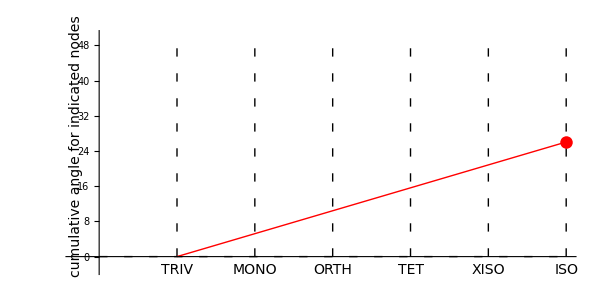

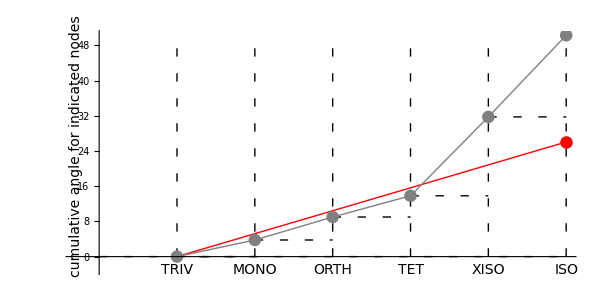

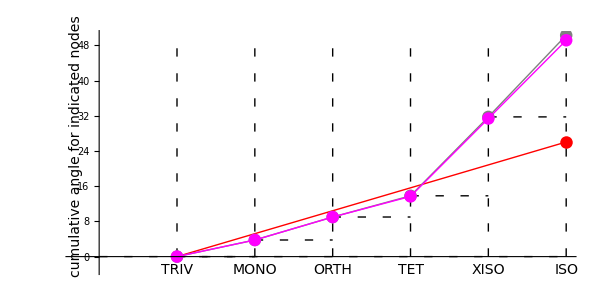

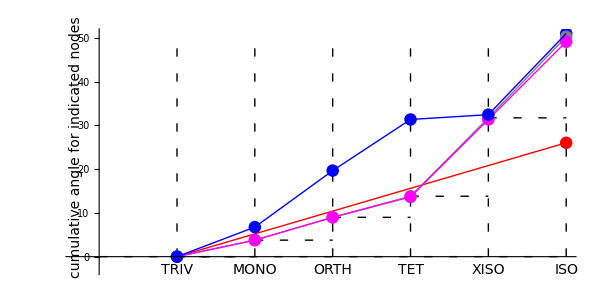

```mathematica
Print[DateSequence[DateList[],"yes"]];
(* WantNM4="noWantNM4";
If[WantNM4=="WantNM4",Print[" UforNM4 = ", MatrixForm[UforNM4]]]; *)
MatrixNote[Tmat]
Print["Node sequence is ",Σn/@domain[Σn]];
Print[" UforNM4 = ", MatrixForm[UforNM4]];
GraphicsForCumulative[Tmat,Σn,"WantNM1","noWantNM2","noWantNM3","noWantNM4"]
GraphicsForCumulative[Tmat,Σn,"WantNM1","WantNM2","noWantNM3","noWantNM4"]
GraphicsForCumulative[Tmat,Σn,"WantNM1","WantNM2","WantNM3","noWantNM4"]
GraphicsForCumulative[Tmat,Σn,"WantNM1","WantNM2","WantNM3","WantNM4"]
```

#### nm1, nm2, nm3, nm4 for four different node sequences

-Graphics-

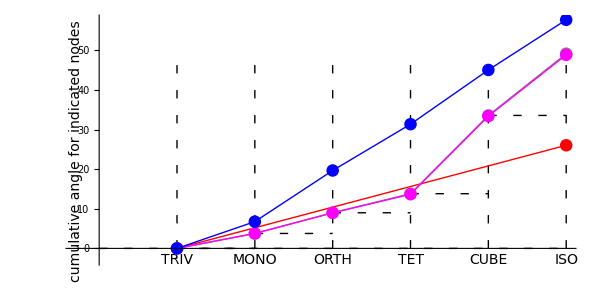

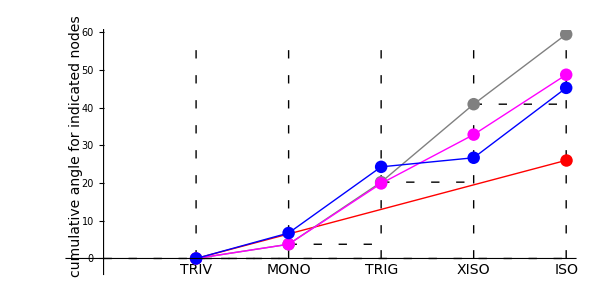

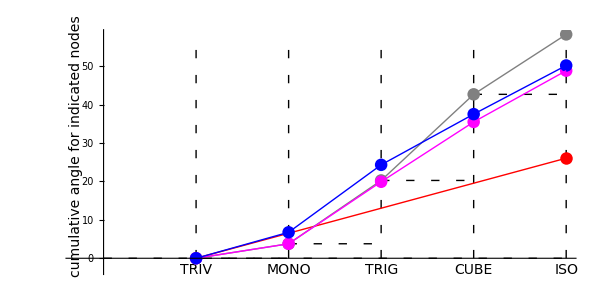

```mathematica
GraphicsForCumulative[Tmat,ΣnTETXISO,"WantNM1","WantNM2","WantNM3","WantNM4"]
GraphicsForCumulative[Tmat,ΣnTETCUBE,"WantNM1","WantNM2","WantNM3","WantNM4"]
GraphicsForCumulative[Tmat,ΣnTRIGXISO,"WantNM1","WantNM2","WantNM3","WantNM4"]
GraphicsForCumulative[Tmat,ΣnTRIGCUBE,"WantNM1","WantNM2","WantNM3","WantNM4"]
```

#### example check for a case (Brown) where nm4 gives a cumulative beta that is lower than nm3

```mathematica
AngleToNextFrom[#,Tmat,ΣnTRIGXISO,nm3]/Degree&/@Drop[domain[ΣnTRIGXISO],-1]
Total[%]
AngleToNextFrom[#,Tmat,ΣnTRIGXISO,nm4]/Degree&/@Drop[domain[ΣnTRIGXISO],-1]
Total[%]
```

{3.77222,16.1286,12.9507,15.8826}

48.7341

{6.75629,17.5483,2.4105,18.5368}

45.252

#### nm1, nm2, nm3, nm4 for one node sequence

-Graphics-

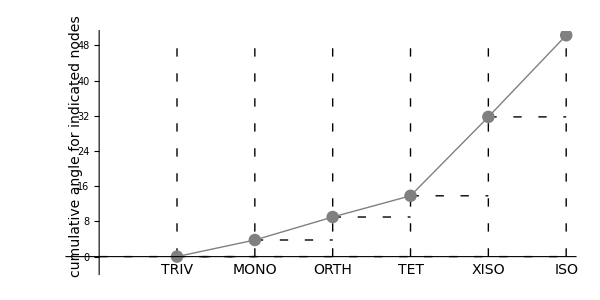

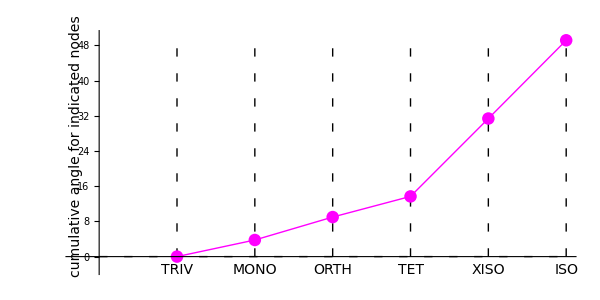

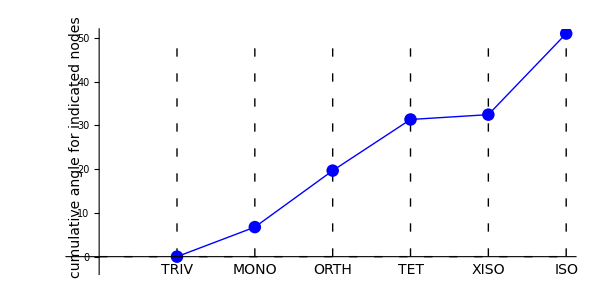

```mathematica
GraphicsForCumulative[Tmat,Σn,"WantNM1","noWantNM2","noWantNM3","noWantNM4"]
GraphicsForCumulative[Tmat,Σn,"noWantNM1","WantNM2","noWantNM3","noWantNM4"]
GraphicsForCumulative[Tmat,Σn,"noWantNM1","WnoantNM2","WantNM3","noWantNM4"]
GraphicsForCumulative[Tmat,Σn,"noWantNM1","noWantNM2","noWantNM3","WantNM4"]
```

#### Difference between Node Modes (3 vs 4 and 3 vs 2)

11-22-2023 16:19

T is Brown

Node sequence is {TRIV,MONO,ORTH,TET,XISO,ISO}

UforNM4 = (0.921451 | -0.368714 | -0.12239
-0.365504 | -0.929543 | 0.0485472
-0.131666 | 0. | -0.991294)

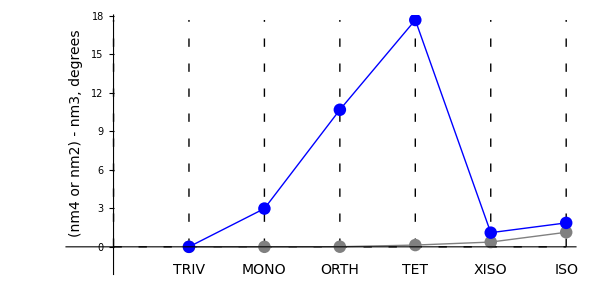

```mathematica
Print[DateSequence[DateList[],"yes"]];
MatrixNote[Tmat]
Print["Node sequence is ",Σn/@domain[Σn]];
Print[" UforNM4 = ", MatrixForm[UforNM4]];
Graphics[{PointSize[.015],
{Dashing[{.01,.02}],
Line[{{0,0},{nMax[Σn],0}}],
Table[Line[{{n,0},{n,dymax[Tmat,Σn,nm4,nm3]/Degree}}],{n,0,nMax[Σn]}]},
{nm2col,Point[{#,ydiff[#,Tmat,Σn,nm2,nm3]/Degree}]&/@domain[Σn], (* points *)
                    Line[{#,ydiff[#,Tmat,Σn,nm2,nm3]/Degree}&/@domain[Σn]]},  (* line *)
{nm4col,Point[{#,ydiff[#,Tmat,Σn,nm4,nm3]/Degree}]&/@domain[Σn], (* points *)
                   Line[{#,ydiff[#,Tmat,Σn,nm4,nm3]/Degree}&/@domain[Σn]]},  (* line *)
Text[Style[Σn[#],14],{#,-0.1dymax[Tmat,Σn,nm4,nm3]/Degree}]&/@domain[Σn],
Text[Style["(nm4 or nm2) - nm3, degrees",14],{-.5,.5dymax[Tmat,Σn,nm4,nm3]/Degree},{0,0},{0,1}]
},
AspectRatio->1/2,ImageSize->600,Ticks->{None,Automatic},Axes->{None,True},GridLines-> None,AxesOrigin->{0,0}]
```

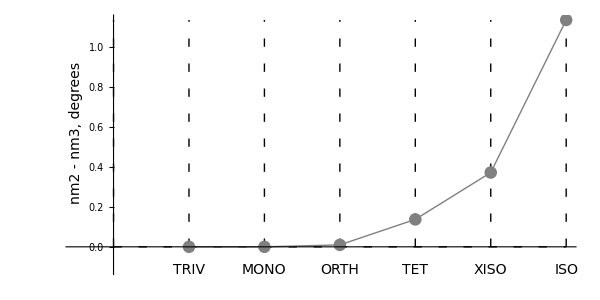

```mathematica
Graphics[{PointSize[.015],
{Dashing[{.01,.02}],
Line[{{0,0},{nMax[Σn],0}}],
Table[Line[{{n,0},{n,dymax[Tmat,Σn,nm2,nm3]/Degree}}],{n,0,nMax[Σn]}]},
{nm2col,Point[{#,ydiff[#,Tmat,Σn,nm2,nm3]/Degree}]&/@domain[Σn], (* points *)
                    Line[{#,ydiff[#,Tmat,Σn,nm2,nm3]/Degree}&/@domain[Σn]]},  (* line *)
Text[Style[Σn[#],14],{#,-0.1dymax[Tmat,Σn,nm2,nm3]/Degree}]&/@domain[Σn],
Text[Style["nm2 - nm3, degrees",14],{-.5,.5dymax[Tmat,Σn,nm2,nm3]/Degree},{0,0},{0,1}]
},
AspectRatio->1/2,ImageSize->600,Ticks->{None,Automatic},Axes->{None,True},GridLines-> None,AxesOrigin->{0,0}]
```

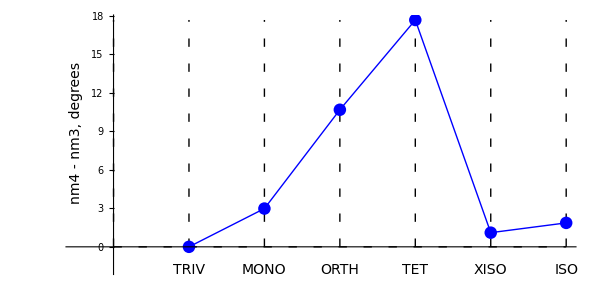

```mathematica
Graphics[{PointSize[.015],
{Dashing[{.01,.02}],
Line[{{0,0},{nMax[Σn],0}}],
Table[Line[{{n,0},{n,dymax[Tmat,Σn,nm4,nm3]/Degree}}],{n,0,nMax[Σn]}]},
{nm4col,Point[{#,ydiff[#,Tmat,Σn,nm4,nm3]/Degree}]&/@domain[Σn], (* points *)
                    Line[{#,ydiff[#,Tmat,Σn,nm4,nm3]/Degree}&/@domain[Σn]]},  (* line *)
Text[Style[Σn[#],14],{#,-0.1dymax[Tmat,Σn,nm4,nm3]/Degree}]&/@domain[Σn],
Text[Style["nm4 - nm3, degrees",14],{-.5,.5dymax[Tmat,Σn,nm4,nm3]/Degree},{0,0},{0,1}]
},
AspectRatio->1/2,ImageSize->600,Ticks->{None,Automatic},Axes->{None,True},GridLines-> None,AxesOrigin->{0,0}]
```